## Lesson

Entity:

```mathematica
Entity["TaxonomicSpecies","SolanumTuberosum::ts937"]
```

potato

Entities in a class:

```mathematica
EntityList[EntityClass["Exoplanet",All]][[1;;5]]
```

{11 Comae Berenices b,11 Ursae Minoris b,14 Andromedae b,14 Herculis b,16 Cygni b}

EntityValue shorthand:

```mathematica
Entity["Country","Switzerland"]["BorderingCountries"]
```

{Austria,France,Germany,Italy,Liechtenstein}

List of properties for an entity type:

```mathematica
EntityProperties[Entity["Country","Austria"]][[1;;5]]
```

{active home listings,adjusted net national income,seasonal bank borrowings from Fed, plus adjustments,regions,adult population}

List of properties for an entity type:

```mathematica
InputForm[Entity["Country","Austria"]]
```

Entity["Country", "Austria"]

## Questions

Q1. Find the flag of Switzerland.

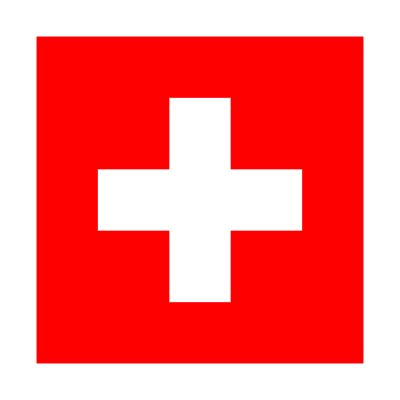

```mathematica
Entity["Country","Switzerland"]["Flag"]
```

Q2. Get an image of an elephant.

```mathematica
Entity["TaxonomicSpecies","LoxodontaAfricana::qtsb3"]["Image"]
```

-Graphics-

Q3. Use the “Mass” property to generate a list of the masses of the planets.

```mathematica
EntityClass["Planet",All]["Mass"]
```

{3.3×10^23 kg,4.867×10^24 kg,5.97×10^24 kg,6.417×10^23 kg,1.898×10^27 kg,5.683×10^26 kg,8.681×10^25 kg,1.024×10^26 kg}

Q4. Make a bar chart of the masses of the planets.

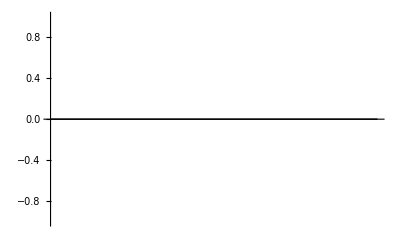

```mathematica
BarChart[EntityClass["Planet",All]["Mass"]]
```

Q5. Make an image collage of images of the planets.

```mathematica
ImageCollage[EntityClass["Planet",All]["Image"]]
```

-Graphics-

Q6. Edge detect the flag of China.

```mathematica
EdgeDetect[Entity["Country","China"]["Flag"]]
```

-Graphics-

Q7. Find the height of the Empire State Building.

```mathematica
Entity["Building","EmpireStateBuilding::h583b"]["Height"]
```

1454.07 ft

Q8. Compute the height of the Empire State Building divided by the height of the Great Pyramid.

```mathematica
(Entity["Building","EmpireStateBuilding::h583b"]["Height"])/(Entity["Building","GreatPyramidOfGiza::jbm66"]["Height"])
```

3.18849

Q9. Compute the elevation of Mount Everest divided by the height of the Empire State Building.

```mathematica
(Entity["Mountain","MountEverest"]["Elevation"])/(Entity["Building","EmpireStateBuilding::h583b"]["Height"])
```

19.9658

Q10. Find the dominant colours in the painting The Starry Night.

```mathematica
DominantColors[Entity["Artwork","TheStarryNight::VincentVanGogh"]["Image"]]
```

{RGBColor[0.3332100732374338, 0.435187461120797, 0.6023100342932706],RGBColor[0.14034756426993764, 0.14880903344144789, 0.1328084785182346],RGBColor[0.4972573447416196, 0.5560651909750424, 0.5124431010476901],RGBColor[0.7205755102806681, 0.6443868305594601, 0.155186863494116]}

Q11. Find the dominant colours in an image collage of the flag images of all countries in Europe.

```mathematica
DominantColors[ImageCollage[#["Flag"]&/@Entity["GeographicRegion","Europe"]["Countries"]]]
```

{RGBColor[0.8154912704343082, 0.07183429501775093, 0.11899881379313884, 1.],RGBColor[0.9986458805056474, 0.9980546836815546, 0.9983063029237315, 1.],RGBColor[0.0026313917181790235, 0.18879568960212262, 0.5517034043661796, 1.],RGBColor[0.07627949265147368, 0.2979124529227281, 0.5661600168974682, 1.],RGBColor[0.9957020082617171, 0.8056773605773195, 0.019856271128652295, 1.],RGBColor[0.9392601550446196, 0.007912187699817226, 0.0023854843018166977, 1.],RGBColor[0.2633724125420227, 0.6754291204335423, 0.8827829231816512, 1.],RGBColor[0.1475288206794519, 0.6079028338887605, 0.2985433504365848, 1.],RGBColor[0.0021235914036969506, 0.00093741840854889, 0.0009352564156712247, 1.],RGBColor[0.621622487879173, 0.18680215386485763, 0.22409839569199513, 1.],RGBColor[0.0014068781545504563, 0.4688856650239858, 0.290951442056169, 1.],RGBColor[0.8128664876552425, 0.652363721066671, 0.2531338234555819, 1.],RGBColor[0.004257201477055596, 0.3988643406075376, 0.0002533115922100898, 1.],RGBColor[0.9891825965908095, 0.46454326967231735, 0.009620246491776811, 1.]}

Q12. Make a pie chart of the GDP of countries in Europe.

```mathematica
PieChart[#["GDP"]&/@Entity["GeographicRegion","Europe"]["Countries"]]
```

-Graphics-

Q13. Add an image of a koala to an image of the Australian flag.

```mathematica
ImageAdd[Entity["TaxonomicSpecies","PhascolarctosCinereus::2kft4"]["Image"],Entity["Country","Australia"]["Flag"]]
```

-Graphics-

## Extended Questions

+Q1. Make an image collage of the flags of all countries in Europe, using the “FlagImage” property.

```mathematica
ImageCollage[#["Flag"]&/@Entity["GeographicRegion","Europe"]["Countries"]]
```

-Graphics-

+Q2. Edge detect an image of the painting The Starry Night.

```mathematica
EdgeDetect[Entity["Artwork","TheStarryNight::VincentVanGogh"]["Image"]]
```

-Graphics-

+Q3. Colour negate the Mona Lisa painting.

```mathematica
ColorNegate[Entity["Artwork","MonaLisa::LeonardoDaVinci"]["Image"]]
```

-Graphics-